# Quantum Mechanics

## An introduction to, and derivation of, the fundamental equations of Schrodinger’s quantum mechanics

## The Wavefunction

The quantum wavefunction is a (L2 normalizable) complex field defined over some continuous space of states. For example, consider a 1D wavefunction of position:

```mathematica
exampleψ[x_] =  ⅇ^(-(-1+x)^4-2 ⅈ π x)+(ⅇ^(-ⅈ ⅇ^(-x^2)-(x-2)^2/2))/π^(1/4) // (#/(√NIntegrate[Abs[#]^2,{x,-∞, ∞}])&);
```

```mathematica
NIntegrate[ Abs[exampleψ[x]]^2,{x, -∞, ∞}]
```

1.

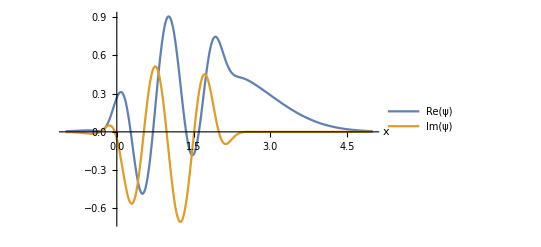

```mathematica
domain = {x, -1, 5};
Plot[
	{Re[exampleψ[x]], Im[exampleψ[x]]}, domain,
	AxesLabel-> {x}, 
	PlotRange -> All,
	PlotLegends-> {Re[ψ], Im[ψ]}
]
```

Although the wavefunction describes a physical system, it is itself unphysical. Only its absolute value squared can be observed.

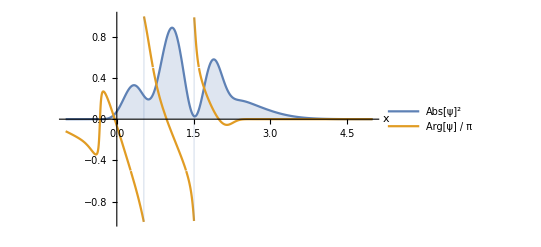

```mathematica
Plot[
	{Abs[exampleψ[x]]^2, Arg[exampleψ[x]]/(π)}, domain,
	AxesLabel-> {x}, 
	PlotRange-> All, 
	Filling -> {1->Axis},
	PlotLegends-> {Abs[ψ]^2, "Arg[ψ] / π"}
]
```

In the Born interpretation, the absolute value squared of the (normalised) wavefunction is a probability density function. If our wavefunction described a particle’s position, an integrated region of the squared norm would give the probability of finding the particle within that region when measured.

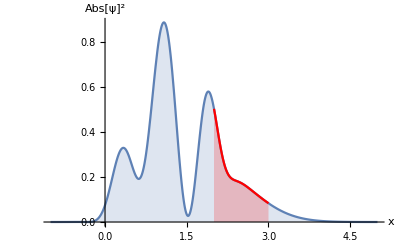
-Graphics-Pr(2 < x < 3) 
= ∫_2^3  |ψ|^2 ⅆx 
=0.196048

```mathematica
Overlay[{
	Plot[{
			Abs[exampleψ[x]]^2, 
			ConditionalExpression[Abs[exampleψ[x]]^2, x > 2 && x < 3]
		}, 
		domain,
		Filling -> Axis,
		AxesLabel-> {x, Abs[ψ]^2},
		PlotStyle -> {Default, Red},
		PlotRange-> All
	],
	Text["Pr(2 < x < 3) \n= ∫_2^3  |ψ|^2 ⅆx \n=" <>
		 ToString[NIntegrate[Abs[exampleψ[x]]^2, {x, 2, 3}]]]
	},
	Alignment -> {0.6, 0}
]
```

Alternatively, if we measured the position of many particles all described by the same wavefunction, we’d expect the distribution to follow the norm squared of that wavefunction.

```mathematica
exampleSamples = RandomVariate[ProbabilityDistribution[Abs[exampleψ[x]]^2, {x, -∞, ∞}], 10^3];
```

```mathematica
Animate[
	Overlay[{
	Show[
		Histogram[exampleSamples[[;;n]], {0.1}, "ProbabilityDensity"],
		Plot[{
					Abs[exampleψ[x]]^2, 
					ConditionalExpression[Abs[exampleψ[x]]^2, x > 2 && x < 3]},
				domain, Filling-> Axis, PlotStyle->{Default, Red}],
		AxesLabel -> {"x", Abs[ψ]^2}, PlotRange -> {0, 1}
	],
		Text[
			"# measurements ∈ [2, 3] \n=" <>
			StringTake[ToString[
				100 N[Count[exampleSamples[[;;n]], u_ /; u > 2 && u < 3] / 
				  If[n > 0, n, 1]]
			], UpTo[4]] <> "%"]},
		Alignment -> {1, 0}],
	{{n, 0, "# measurements"}, 0, Length[exampleSamples], 1}
]
```

The probability density function alone however is an incomplete description of the system. The complex phase is very important; we’ll here-forth indicate it by colour.

```mathematica
plotWavefunction[psi_, {r_, range__}, showbar_:True] :=
	Plot[
		Abs[psi]^2, {r, range}, 
		AxesLabel -> {r, Abs[ψ]^2},
		PlotRange -> All,
		ColorFunction -> (ColorData["Rainbow"][Rescale[Arg[psi /. r -> #], {-π, π}]] &),
		ColorFunctionScaling -> False,
		Filling -> Axis,
		PlotLegends -> If[showbar == True, BarLegend["Rainbow", LegendLabel -> "arg[ψ] / 2π"], None]
	] /.
		Line[pts_, _] :> {Black, Line[pts]}
```

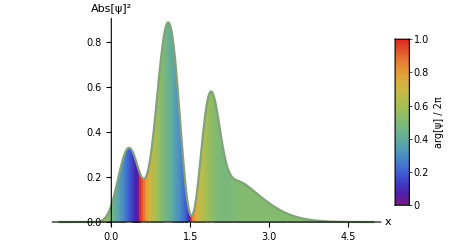

```mathematica
plotWavefunction[exampleψ[x], domain]
```

The complex phase governs the evolution of the wavefunction. A phase gradient indicates a probability current; that the probability density function (and the likelihood our particle will appear in a given region) will change in time.

```mathematica
Off[NDSolveValue::bcart]
```

```mathematica
simulateWavefunction[psi_, potential_, {r_, domain__}, {_, times__}] :=
	NDSolveValue[
		{ⅈ Derivative[0,1][ψ][r, τ] == Derivative[2,0][ψ][r, τ] / 2 + ψ[r, τ] potential, ψ[r, 0] == psi},
		ψ, {r, domain}, {τ, times}
	]
```

```mathematica
exampleψ[space_, time_] =
	simulateWavefunction[exampleψ[x], 0, {x, -2, 8}, {t, 0, 0.3}][space, time];
```

```mathematica
Animate[
	Overlay[
		{Show[
			plotWavefunction[exampleψ[x, t], domain, False],
			Plot[Abs[exampleψ[x, t]]^2,
				{x, 2, 3}, Filling -> Axis,
				PlotRange -> {0, 1.2},
				PlotStyle -> Red]],
		 Text[
			Style[
				"Pr(2 < x < 3) \n= " <>
				ToString[NIntegrate[Abs[exampleψ[x, t]]^2, {x, 2, 3}]], 
				Black]]},
		Alignment->{0.8, 0}],
	{t, 0, 0.3}
]
```

This was an example of a free system. Its evolution, and the evolution of general trapped systems, is determined by the Schrodinger equation.

## The Schrodinger Equation

For a system with total energy given encoded in the Hamiltonian operator Ĥ, the time-dependent Schrodinger equation is

```mathematica
i ℏ Derivative[0,1][ψ][r,t]==Ĥ[ψ[r,t]]
```

i ℏ ψ^(0,1)[r,t]==Ĥ[ψ[r,t]]

### Hamiltonian Decomposition

```mathematica
(* Schrod preserves L2 norm *)
```

```mathematica
hamiltonian[psi_, potential_, r_] := 
	-1/2 D[psi, {r,2}] + potential psi
```

## Quantum Tunnelling

The Schrodinger evolution of the wavefunction enables particles to be appear in classically forbidden regions. Consider some waveform ∝ e^(-2 x^2), kicked by a phase gradient e^(-ⅈ x), approaching a potential barrier.

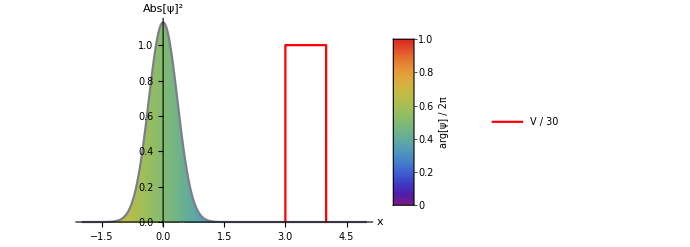

```mathematica
incidentψ[x_] = (√2)/π^(1/4)Exp[- 2 x^2]Exp[- ⅈ x]; 
stepHeight = 30;
stepV[x_] = stepHeight (UnitStep[x-3] - UnitStep[x-4]);

Show[
	plotWavefunction[ incidentψ[x], {x, -2, 5} ],
	Plot[
		stepV[x]/stepHeight, 
		{x,2.99, 4.01}, 
		Exclusions->None, 
		PlotStyle->{Thick, Red},
		PlotLegends->{"V / " <> ToString[stepHeight]}]
]
```

This wavefunction has an expectation energy much lower than the height of the potential.

```mathematica
expectedEnergy[psi_, potential_,  r_] :=
	Integrate[
		(Conjugate[psi] /. Conjugate[r] -> r)
		(hamiltonian[psi, potential, r]),
		{r, -∞, ∞}
	]
```

```mathematica
expectedEnergy[incidentψ[x], 0, x]
```

3/2

In a classical analog, this would mean the particle cannot be found beyond the potential barrier. However, when we evolve the wavefunction through time...

```mathematica
Off[NDSolveValue::eerr]
```

```mathematica
endTime = 1.8;
incidentψ[space_, time_] =
	simulateWavefunction[incidentψ[x], stepV[x], {x, -6, 12}, {t, 0, endTime}][space, time];
```

```mathematica
Animate[
	Show[
		plotWavefunction[
			incidentψ[x, t], 
			{x, -3, 8}, 
			False],
		Plot[stepV[x]/stepHeight,{x,2.99, 4.01}, Exclusions->None, PlotStyle->{Thick, Red}]],
	{t, 0,endTime}
]
```

a non-negligible wavefunction amplitude emerges beyond the barrier, after exponentially decaying within the barrier.

```mathematica
transmittedψ[x_] = incidentψ[x, endTime];
transmittedSamples = RandomVariate[ProbabilityDistribution[Abs[transmittedψ[x]]^2, {x, -∞, ∞}], 10^3];
```

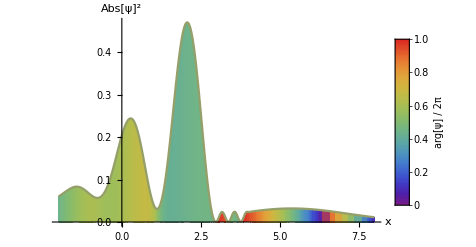

```mathematica
plotWavefunction[transmittedψ[x], {x, -2, 8}]
```

```mathematica
Animate[
	Overlay[{
	Show[
		Histogram[transmittedSamples[[;;n]], {0.1}, "ProbabilityDensity"],
		Plot[{
					Abs[transmittedψ[x]]^2, 
					ConditionalExpression[Abs[transmittedψ[x]]^2, x > 2 && x < 3]},
				domain, Filling-> Axis, PlotStyle->{Default, Red}],
		AxesLabel -> {"x", Abs[ψ]^2}, PlotRange -> {0, 1}
	],
		Text[
			"# measurements ∈ [2, 3] \n=" <>
			StringTake[ToString[
				100 N[Count[transmittedSamples[[;;n]], u_ /; u > 2 && u < 3] / 
				  If[n > 0, n, 1]]
			], UpTo[4]] <> "%"]},
		Alignment -> {1, 0}],
	{{n, 0, "# measurements"}, 0, Length[transmittedSamples], 1}
]
```

## The Quantum Harmonic Oscillator

```mathematica
(* modes *)
```

```mathematica
(* propping modes *)
```

```mathematica
(* decomposing into modes *)
```

```mathematica
(* coherent mode by translation *)
```

```mathematica
(* decomposing coherent onto modes *)
```